# Práctica 2: Autómatas Celulares

### Javier Rodríguez Domínguez y Jaime Ferrando Huertas

## II – Reconocedores de Lenguajes

## Ejercicio 1:

Implemente un módulo en Mathematica que, tomando como entrada un AFD proporcione como salida un AC unidireccional unidimensional que acepte el mismo lenguaje que el AFD mediante entrada paralela.

```mathematica
(*módulo para transformar un AFD en un autómata celular*)
AfdToAc[automata_]:=Module[{states,symbols,transitions,rules,i,j,final},
states=automata[[1]];
symbols = automata[[2]];
transitions =automata[[3]];
final = automata[[5]];
rules = {};
(*creamos una regla por cada combinación de estados existente*)
For[i=1,i≤Length[states],i++,
For[j=1,j≤Length[states],j++,
AppendTo[rules,{states[[i]],states[[j]],states[[j]]}];
];
];
(*creamos una regla por cada combinación de simbolos existente*)
For[i=1,i≤Length[symbols],i++,
For[j=1,j≤Length[symbols],j++,
AppendTo[rules,{symbols[[i]],symbols[[j]],symbols[[j]]}];
];
];
(*creamos una regla por transición*)
For[i=1,i≤Length[transitions],i++,
AppendTo[rules,transitions[[i]]];
];
(*devolvemos el autómata formateado*)
Return[{Union[states],Union[rules],Union[final]}];
];
```

```mathematica
sampleAutomata = {{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},{q},{r}}
```

{{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},{q},{r}}

```mathematica
sampleCelular = AfdToAc[sampleAutomata]
```

{{p,q,r},{{a,a,a},{a,b,b},{b,a,a},{b,b,b},{p,a,r},{p,b,q},{p,p,p},{p,q,q},{p,r,r},{q,a,p},{q,b,r},{q,p,p},{q,q,q},{q,r,r},{r,a,r},{r,b,r},{r,p,p},{r,q,q},{r,r,r}},{r}}

## Ejercicio 2:

Implemente un módulo Mathematica que, tomando como entrada una cadena arbitraria, un AC que reconoce un lenguaje mediante entrada paralela en tiempo real y un estado de frontera q S, proporcione como salida True si el AC acepta la cadena y False en caso contrario.

```mathematica
(*Módulo para calcular el siguiente estado de una cadena de forma unidireccional*)
NextConfigOneWay[estado_,regla_]:=Module[{lenestado,i,doblete,sol,result},
lenestado = Length[estado];
sol = {};
(*se calcula el resultado de cada célula tneiendo en cuenta a ella y la de su izquierda*)
(*la celda 1 no se tiene en cuenta, ya que es la barrera*)
For[i=2,i≤lenestado,i++,
doblete= {estado[[i-1]],estado[[i]],_};
result = Cases[regla,doblete];
AppendTo[sol,result[[1]][[3]]];
];
sol=Prepend[sol,estado[[1]]];
(*se devuelve la nueva cadena*)
Return[sol];
];
```

```mathematica
(*Módulo que, dado un autómata, una palabra y un símolo que actua de barrera devuelve si el automata reconoce la palabra*)
ReconoceRPOCA[ac_,palabra_,q_]:=Module[{s,rules,splus,n,word,i},
s=ac[[1]];
rules = ac[[2]];
splus = ac[[3]];
n = Length[palabra];
word = Prepend[palabra,q];
(*se calculan tantas iteraciones como longitud de la palabra*)
For[i=1,i≤n,i++,
word = NextConfigOneWay[word,rules];
];
(*se devuelve si el símbolo de salida pertenece a el conjunto de finales*)
Return [MemberQ[splus,word[[n+1]]]];
];
```

```mathematica
ReconoceRPOCA[sampleCelular,{a,b,a,a,b},q]
```

True

```mathematica
ReconoceRPOCA[sampleCelular,{a,b,a,b,a},q]
```

False

## Ejercicio 3:

Proporcione una construcción formal para obtener a partir de un AFD, un AC equivalente unidimensional bidireccional (vecindario {-1,0,1}) con entrada paralela. Implemente un módulo en Mathematica que lleve a cabo la construcción propuesta.

```mathematica
(*módulo para transformar un AFD en un autómata celular con entrada bidireccional*)
AfdToAcBidi[automata_]:=Module[{states,symbols,celular,final,rules,allsymbols,newrules,i,k},
symbols=automata[[2]];
(*claculamos el automata celular unidireccional para el AFD de entrada*)
celular=AfdToAc[automata];
states=celular[[1]];
rules=celular[[2]];
final=celular[[3]];
(*vemos todos los símbolos y estados que lo componen*)
allsymbols=Union[states,Flatten[rules]];
newrules={};
(*para cada una de las reglas del automata unidireccional*)
For[i=1,i≤Length[rules],i++,
(*añadimos todas los combinaciones de símbolos en el lado derecho, así siempre se reconocerá como es debido, independientemente del símbolo a la derecha del centro*)
For[k=1,k≤Length[allsymbols],k++,
AppendTo[newrules,{rules[[i]][[1]],rules[[i]][[2]],allsymbols[[k]],rules[[i]][[3]]}];
];
];
(*se devuelve el autómata bidireccional*)
Return[{Union[states],Union[newrules],Union[final]}];
];
```

```mathematica
sampleCelular = AfdToAcBidi[sampleAutomata]
```

{{p,q,r},{{a,a,a,a},{a,a,b,a},{a,a,p,a},{a,a,q,a},{a,a,r,a},{a,b,a,b},{a,b,b,b},{a,b,p,b},{a,b,q,b},{a,b,r,b},{b,a,a,a},{b,a,b,a},{b,a,p,a},{b,a,q,a},{b,a,r,a},{b,b,a,b},{b,b,b,b},{b,b,p,b},{b,b,q,b},{b,b,r,b},{p,a,a,r},{p,a,b,r},{p,a,p,r},{p,a,q,r},{p,a,r,r},{p,b,a,q},{p,b,b,q},{p,b,p,q},{p,b,q,q},{p,b,r,q},{p,p,a,p},{p,p,b,p},{p,p,p,p},{p,p,q,p},{p,p,r,p},{p,q,a,q},{p,q,b,q},{p,q,p,q},{p,q,q,q},{p,q,r,q},{p,r,a,r},{p,r,b,r},{p,r,p,r},{p,r,q,r},{p,r,r,r},{q,a,a,p},{q,a,b,p},{q,a,p,p},{q,a,q,p},{q,a,r,p},{q,b,a,r},{q,b,b,r},{q,b,p,r},{q,b,q,r},{q,b,r,r},{q,p,a,p},{q,p,b,p},{q,p,p,p},{q,p,q,p},{q,p,r,p},{q,q,a,q},{q,q,b,q},{q,q,p,q},{q,q,q,q},{q,q,r,q},{q,r,a,r},{q,r,b,r},{q,r,p,r},{q,r,q,r},{q,r,r,r},{r,a,a,r},{r,a,b,r},{r,a,p,r},{r,a,q,r},{r,a,r,r},{r,b,a,r},{r,b,b,r},{r,b,p,r},{r,b,q,r},{r,b,r,r},{r,p,a,p},{r,p,b,p},{r,p,p,p},{r,p,q,p},{r,p,r,p},{r,q,a,q},{r,q,b,q},{r,q,p,q},{r,q,q,q},{r,q,r,q},{r,r,a,r},{r,r,b,r},{r,r,p,r},{r,r,q,r},{r,r,r,r}},{r}}

## Ejercicio 4:

Implemente un módulo Mathematica que muestre la secuencia de computación que se lleva a cabo en el módulo propuesto en la actividad (2) mediante un diagrama espaciotemporal.

```mathematica
(*módulo para imprimir el diagrama espaciotemporal de la computación de una palabra por un automata celular unidimensional*)
RPOCAPlot [ac_,palabra_,q_]:=Module[{s,rules,splus,n,word,i,print,items,colors,colorpattern},
s=ac[[1]];
rules = ac[[2]];
splus = ac[[3]];
n = Length[palabra];
(*añadimos el símbolo de barrera al principio de la palabra*)
word = Prepend[palabra,q];
print ={};
(*a la hora de imprimir la palabra, quitamos la barrera*)
PrependTo[print,Rest[word]];
(*por cada símbolo de la palabra hacemos una iteración*)
For[i=1,i≤n,i++,
word = NextConfigOneWay[word,rules];
PrependTo[print,Rest[word]];
];
(*generamos tantos colores como simbolos diferentes existan*)
items=Union[Flatten[rules]];
colors=ColorList[Length[items]];
colorpattern = {};
(*a cada símbolo le asignamos un color diferente*)
For[i=1,i≤Length[items],i++,
AppendTo[colorpattern,items[[i]]->colors[[i]]];
];
(*imprimimos la computación de la palabra usando los colores*)
Return [{ArrayPlot[print,ColorRules->colorpattern], colorpattern}];
];
```

```mathematica
(*módulo para generar un número dado de colores*)
ColorList[numb_]:=Module[{sol,i,j,k,increase,parts},
(*calculamos los incrementos*)
parts =Floor[CubeRoot[numb-1]];
increase = 1/parts;
sol={};
(*aumentamos cada uno de los valores RGB segun el incremento*)
For[i=0,i≤1,i=i+increase,
For[j=0,j≤1,j=j+increase,
For[k=0,k≤1,k=k+increase,
AppendTo[sol,{RGBColor[i,j,k]}];
];
];
];
(*los devolvemos en orden aleatorio*)
Return[RandomSample[sol]];
];
```

```mathematica
ColorList[28]
```

{{RGBColor[0, Rational[1, 3], 0]},{RGBColor[Rational[1, 3], 0, Rational[1, 3]]},{RGBColor[0, Rational[2, 3], Rational[2, 3]]},{RGBColor[Rational[1, 3], Rational[2, 3], 1]},{RGBColor[Rational[2, 3], 1, Rational[2, 3]]},{RGBColor[Rational[2, 3], Rational[2, 3], Rational[2, 3]]},{RGBColor[0, 1, 0]},{RGBColor[0, Rational[1, 3], Rational[1, 3]]},{RGBColor[1, 1, Rational[2, 3]]},{RGBColor[Rational[2, 3], 1, 1]},{RGBColor[0, 1, 1]},{RGBColor[0, Rational[2, 3], Rational[1, 3]]},{RGBColor[1, 0, Rational[1, 3]]},{RGBColor[1, 1, Rational[1, 3]]},{RGBColor[Rational[1, 3], 1, Rational[2, 3]]},{RGBColor[Rational[2, 3], 1, 0]},{RGBColor[Rational[2, 3], 0, Rational[1, 3]]},{RGBColor[Rational[1, 3], 0, Rational[2, 3]]},{RGBColor[Rational[2, 3], 1, Rational[1, 3]]},{RGBColor[Rational[2, 3], Rational[2, 3], Rational[1, 3]]},{RGBColor[Rational[1, 3], 0, 1]},{RGBColor[Rational[2, 3], Rational[1, 3], Rational[1, 3]]},{RGBColor[Rational[1, 3], 1, 0]},{RGBColor[Rational[1, 3], Rational[2, 3], Rational[1, 3]]},{RGBColor[Rational[2, 3], Rational[2, 3], 0]},{RGBColor[Rational[2, 3], Rational[1, 3], 1]},{RGBColor[Rational[1, 3], Rational[1, 3], 1]},{RGBColor[Rational[2, 3], Rational[2, 3], 1]},{RGBColor[0, 1, Rational[2, 3]]},{RGBColor[1, Rational[2, 3], 1]},{RGBColor[Rational[2, 3], Rational[1, 3], 0]},{RGBColor[0, 0, 1]},{RGBColor[Rational[1, 3], 1, Rational[1, 3]]},{RGBColor[1, Rational[1, 3], 0]},{RGBColor[0, Rational[1, 3], 1]},{RGBColor[Rational[2, 3], 0, 0]},{RGBColor[0, 0, 0]},{RGBColor[0, 0, Rational[1, 3]]},{RGBColor[Rational[1, 3], Rational[2, 3], Rational[2, 3]]},{RGBColor[0, 0, Rational[2, 3]]},{RGBColor[1, Rational[2, 3], Rational[2, 3]]},{RGBColor[0, Rational[1, 3], Rational[2, 3]]},{RGBColor[1, 1, 0]},{RGBColor[1, 1, 1]},{RGBColor[1, 0, 1]},{RGBColor[1, 0, 0]},{RGBColor[1, Rational[1, 3], Rational[2, 3]]},{RGBColor[0, Rational[2, 3], 1]},{RGBColor[Rational[1, 3], 0, 0]},{RGBColor[0, 1, Rational[1, 3]]},{RGBColor[0, Rational[2, 3], 0]},{RGBColor[Rational[1, 3], Rational[1, 3], Rational[1, 3]]},{RGBColor[1, Rational[1, 3], 1]},{RGBColor[Rational[1, 3], Rational[1, 3], 0]},{RGBColor[Rational[2, 3], 0, Rational[2, 3]]},{RGBColor[1, Rational[1, 3], Rational[1, 3]]},{RGBColor[Rational[1, 3], Rational[2, 3], 0]},{RGBColor[Rational[2, 3], 0, 1]},{RGBColor[1, Rational[2, 3], Rational[1, 3]]},{RGBColor[Rational[2, 3], Rational[1, 3], Rational[2, 3]]},{RGBColor[1, 0, Rational[2, 3]]},{RGBColor[Rational[1, 3], Rational[1, 3], Rational[2, 3]]},{RGBColor[Rational[1, 3], 1, 1]},{RGBColor[1, Rational[2, 3], 0]}}

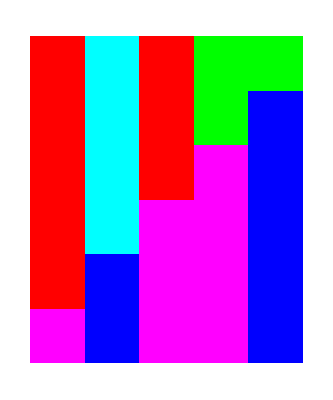
{-Graphics-,{a→{RGBColor[1, 0, 1]},b→{RGBColor[0, 0, 1]},p→{RGBColor[1, 0, 0]},q→{RGBColor[0, 1, 1]},r→{RGBColor[0, 1, 0]}}}

```mathematica
RPOCAPlot[sampleCelular,{a,b,a,a,b},q]
```

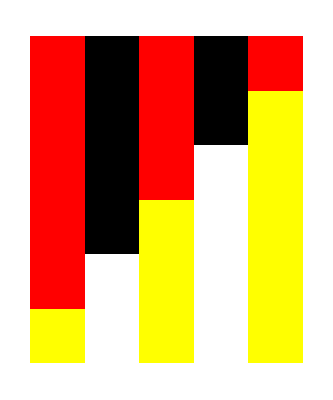
{-Graphics-,{a→{RGBColor[1, 1, 0]},b→{RGBColor[1, 1, 1]},p→{RGBColor[1, 0, 0]},q→{RGBColor[0, 0, 0]},r→{RGBColor[0, 0, 1]}}}

```mathematica
RPOCAPlot[sampleCelular,{a,b,a,b,a},q]
```